# DS Rate Study

## Setup: The Rate, the Delay and the Mass Distribution

## Star Formation Rate

It is logic to assume that BH merges are proportional to the Star Formation Rate (SFR). We use the Mandau function ψ that is in M_⊙Mpc^-3 yr^-1

```mathematica
ψ[z_]:=0.015*(1+z)^2.7/(1+((1+z)/2.9)^5.6)
```

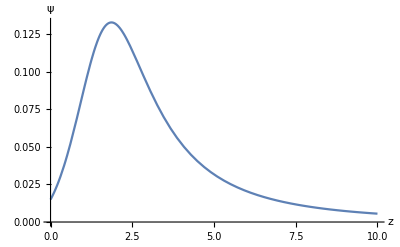

```mathematica
Plot[ψ[z],{z,0,10},AspectRatio->1/GoldenRatio,AxesLabel->{z,ψ}]
```

## Set the Cosmology

```mathematica
H0=70
```

70

```mathematica
tH=1000./H0
```

14.2857

```mathematica
Ωk=0;
```

```mathematica
Ωr=0.00008
```

0.00008

```mathematica
Ωm=0.3
```

0.3

```mathematica
Ωl=1-Ωm-Ωr
```

0.69992

## Delay Function

Now that we have a SFR, we need to wait the natural life of the star in order to have some BBH. This is the ‘delay’. The delay can be modeled by an exponential decay but, for low probability, we can use 1/t as a good approximation. This t must be greater than the life of the star so t>tmin. In principle we have to take into account also the merging time for which we can not detect the  merging i.e. low and very low frequency but, since this lapse of time is negligible compared to the stellar life time,  we will ignore that .

```mathematica
EE[z_]:=(Ωm*(1+z)^3+Ωr*(1+z)^4+Ωk*(1+z)^2+Ωl)^(1/2)
```

```mathematica
cosmictime[z_]:=NIntegrate[tH/((1+x)*EE[x]),{x,z,+∞}]
```

```mathematica
zoft[t_]:=InverseFunction[cosmictime][t]
```

### Useful blocks

```mathematica
zd01=zoft[0.1]
```

29.9249

```mathematica
zd05=zoft[0.5]
```

9.62376

```mathematica
zd2=zoft[2.]
```

3.20909

```mathematica
zd10=zoft[10.]
```

0.329414

```mathematica
tmin=2
```

2

```mathematica
poft[t_]:=Piecewise[{{1,t<tmin},{1*tmin/t,t≥tmin}}]
```

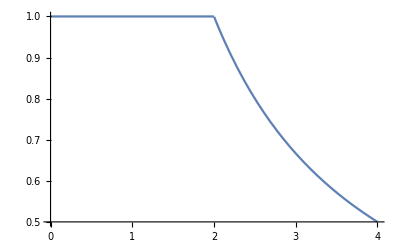

```mathematica
Plot[poft[t],{t,0,4}]
```

```mathematica
zd=6
```

6

```mathematica
cosmictime[zd]
```

0.935326

```mathematica
cosmictime[7]
```

0.765558

```mathematica
deltime[z_]:=NIntegrate[tH/((1+x)*EE[x]),{x,z,zd},WorkingPrecision->MachinePrecision]
```

```mathematica
deltime[29]
```

-0.830634

```mathematica
delay[z_]:=Piecewise[{{1,z<  zd},{cosmictime[zd]/cosmictime[z],z≥ zd}}]
```

```mathematica
delay[0]
```

1

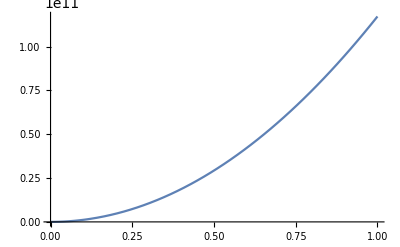

```mathematica
Plot[delay[z],{z,0,10000000}]
```

## GW Rate

Now we can compute the GW rate. We need a prescription for t(z) in order to have an integral over z.

```mathematica
(*RGW[z_]=μ*Integrate[-ψ[x]*1/teff*tH/((1+x)EE[x]),{x,z,+∞}] *) (*This is ok but is slow. A faster version below*)
```

```mathematica
(*RGW[from_]:=(int=μ*NIntegrate[-ψ[x]*1/teff*tH/((1+x)EE[x]),x];
Limit[int,x->+∞]-Limit[int,x->from])*)
```

### Evaluating the GW Rate & the Normalization

```mathematica
μ=25/NIntegrate[-ψ[x]*1/delay[0]*tH/((1+x)EE[x]),{x,0,∞},WorkingPrecision->MachinePrecision]
```

-30.9865

```mathematica
RGW[z_]:=μ*NIntegrate[-ψ[x]*1/delay[z] *tH/((1+x)EE[x]),{x,z,∞},WorkingPrecision->MachinePrecision]
```

```mathematica
RGW[0]
```

25.

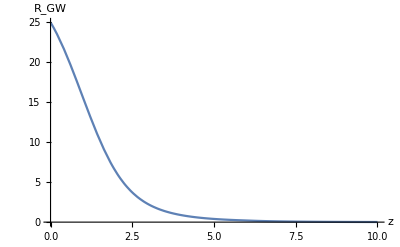

```mathematica
Plot[{RGW[z]},{z,0,10},AspectRatio->1/GoldenRatio,AxesLabel->{z,Subscript[R, GW]},PlotRange->All]
```

```mathematica
Plot[Evaluate@Table[RGW[z,zd],{zd,29.}],{z,0,10}]
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand -(0.214286 (1+x)^1.7)/(√(0.69992+0.3 (1+x)^3+0.00008 (1+x)^4) (1+0.00257378 (1+x)^5.6) (Piecewise[{{NIntegrate[14.2857 Power[«2»],{x,z,1}], z≤1}, {0., z>1}, {0, True}}])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+z}}.

NIntegrate::inumr: The integrand -(0.214286 (1+x)^1.7)/(√(0.69992+0.3 (1+x)^3+0.00008 (1+x)^4) (1+0.00257378 (1+x)^5.6) (Piecewise[{{NIntegrate[14.2857 Power[«2»],{x,z,2}], z≤2}, {0., z>2}, {0, True}}])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+z}}.

NIntegrate::inumr: The integrand -(0.214286 (1+x)^1.7)/(√(0.69992+0.3 (1+x)^3+0.00008 (1+x)^4) (1+0.00257378 (1+x)^5.6) (Piecewise[{{NIntegrate[14.2857 Power[«2»],{x,z,3}], z≤3}, {0., z>3}, {0, True}}])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+z}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.